```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data = RandomVariate[StudentTDistribution[μ,σ1,ν1],{5}];
```

```mathematica
data
```

{74.7648,96.2762,107.89,98.0402,100.648}

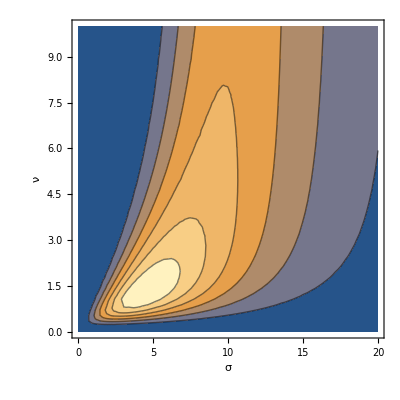

```mathematica
g1=ContourPlot[Likelihood[StudentTDistribution[100,σ,ν],data],{σ,0,20},{ν,0,10},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"σ","ν"},BaseStyle->Medium]
```

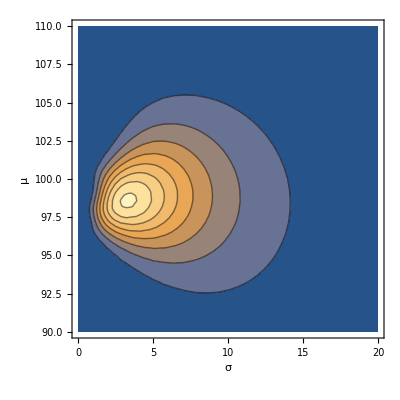

```mathematica
g2=ContourPlot[Likelihood[StudentTDistribution[μ,σ,ν1],data],{σ,0,20},{μ,90,110},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"σ","μ"},BaseStyle->Medium]
```

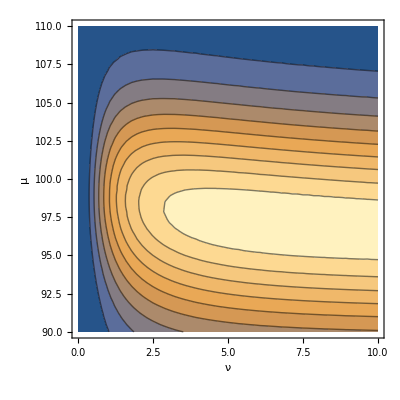

```mathematica
g3=ContourPlot[Likelihood[StudentTDistribution[μ,σ1,ν],data],{ν,0,10},{μ,90,110},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"ν","μ"},BaseStyle->Medium]
```

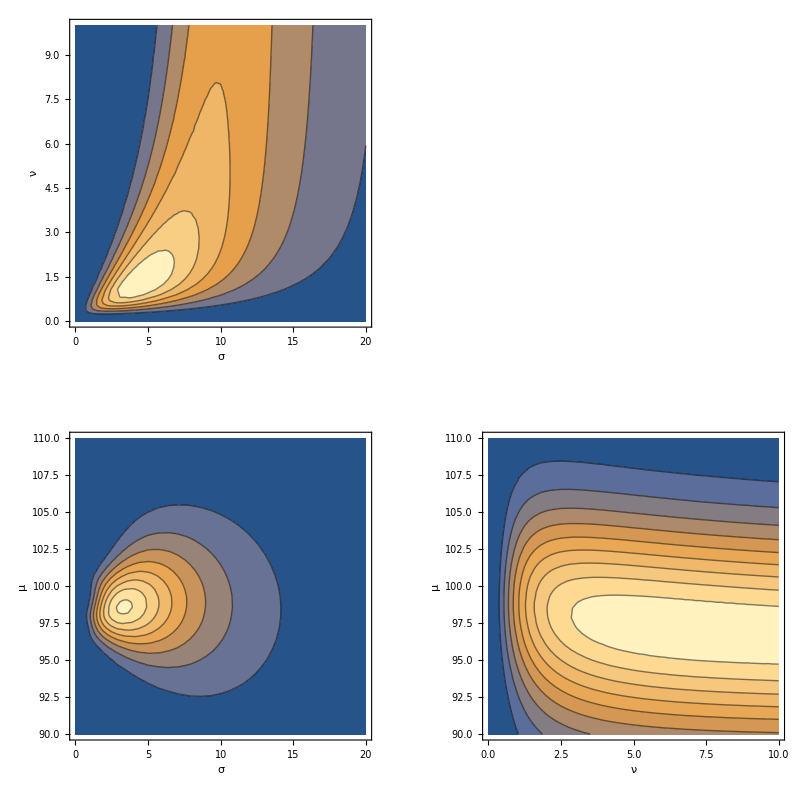

```mathematica
gFinal=Show[GraphicsGrid[{{g1,},{g2,g3}}],ImageSize->800]
```

```mathematica
Export["Distributions_tArithmeticLikelihood.pdf",gFinal]
```

Distributions_tArithmeticLikelihood.pdf